```mathematica
(*LAB 4 image processing*)
```

```mathematica
(*Setting*)
```

```mathematica
SetOptions[{ListPlot3D,Histogram,Plot},ImageSize->Small];
```

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
(*Folder Set up*)
```

```mathematica
SetDirectory["/Users/ornnicha/Documents/docmine/CSS221/LAB5/L5_Lab4/Lab4"]
```

/Users/ornnicha/Documents/docmine/CSS221/LAB5/L5_Lab4/Lab4

```mathematica
(* Pls change SetDirectory *)
```

```mathematica
(*--------------------Part 1--------------------*)
```

```mathematica
(*Problem 1*)
```

```mathematica
T0 := Import["val_2022.png"]
```

```mathematica
ImageDimensions[T0]
```

{101,102}

```mathematica
ImageChannels[T0]
```

3

```mathematica
(*Problem 2*)
```

```mathematica
T1 = RemoveAlphaChannel[T0]
```

-Graphics-

```mathematica
{TG = ColorConvert[T1,"Grayscale"]}
```

{-Graphics-}

```mathematica
(*Problem 3*)
```

```mathematica
{CR,CG,CB} = ColorSeparate[T1]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{T3 = ColorCombine[{CG,CR,CB}]}
```

{-Graphics-}

```mathematica
M3 = ImageData[CR];
```

```mathematica
ListPlot3D[M3,ImageSize->Small]
```

-Graphics3D-

```mathematica
{M3Im = Image[M3]}
```

{-Graphics-}

```mathematica
(*Problem 4*)
```

```mathematica
T4 := Import["baboon.jpg"]
```

```mathematica
{CR,CG,CB} = ColorSeparate[T4]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{T4 = ColorCombine[{CR}]}
```

{-Graphics-}

```mathematica
{T4 = ColorCombine[{CG}]}
```

{-Graphics-}

```mathematica
{T4 = ColorCombine[{CB}]}
```

{-Graphics-}

```mathematica
{T4 = ColorCombine[{CG,CR,CB}],T4 = ColorCombine[{CR,CG,CB}]}
```

{-Graphics-,-Graphics-}

```mathematica
(*Problem 5*)
```

```mathematica
T5 = Import["textold.jpg"]
```

-Graphics-

```mathematica
ImageDimensions[T5]
```

{332,254}

```mathematica
T5gl := ColorConvert[T5,"Grayscale"]
```

```mathematica
{T5gl}
```

{-Graphics-}

```mathematica
T5b := Binarize[T5gl,0.2];
```

```mathematica
{T5b}
```

{-Graphics-}

```mathematica
(*Problem 6*)
```

```mathematica
{Dynamic[Binarize[T5gl,Tre]]}
```

{}

```mathematica
{Slider[Dynamic[Tre],Background->LightBlue],Dynamic[Tre]}
```

{,}

```mathematica
Tr6 = FindThreshold[T5gl]
```

0.301961

```mathematica
T6 := Binarize[T5gl,Tr6]
```

```mathematica
{T6}
```

{-Graphics-}

```mathematica
(*Problem 7*)
```

```mathematica
T7 := Import["river1.JPG"]
```

```mathematica
{T7}
```

{-Graphics-}

```mathematica
T7gl := ColorConvert[T7,"Grayscale"]
```

```mathematica
{T7gl}
```

{-Graphics-}

```mathematica
T7ng := ColorNegate[T7gl]
```

```mathematica
{T7ng}
```

{-Graphics-}

```mathematica
{Dynamic[Binarize[T7ng,Tr7]]}
```

{}

```mathematica
{Slider[Dynamic[Tr7],Background->LightBlue],Dynamic[Tr7]}
```

{,}

```mathematica
{Dynamic[T7b := Binarize[T7ng,Tr7]]}
```

{}

```mathematica
{T7b}
```

{-Graphics-}

```mathematica
Rf7 = Flatten[ImageData[T7ng]];
```

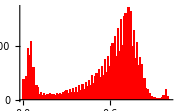

```mathematica
HP = Histogram[Rf7,{0.01},ChartStyle->Red]
```

```mathematica
{Slider[Dynamic[TreP],Background->LightBlue],Dynamic[TreP]}
```

{,}

```mathematica
Dynamic[Show[HP,ListPlot[{{TreP,0}},PlotStyle->PointSize[0.06]]]]
```

```mathematica
{Rh7= Dynamic[Binarize[T7ng,TreP]]}
```

{}

```mathematica
(*Problem 8*)
```

```mathematica
T8 = Import["Heavy_load_noisy.jpg"]
```

-Graphics-

```mathematica
ImageChannels[T8]
```

3

```mathematica
T8 = ColorConvert[T8,"Grayscale"]
```

-Graphics-

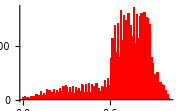

```mathematica
HP8 = Histogram[Flatten[ImageData[T8]],{0.01},ChartStyle->Red]
```

```mathematica
{Slider[Dynamic[TreP8],Background->LightBlue],Dynamic[TreP8]}
```

{,}

```mathematica
Dynamic[Show[HP8,ListPlot[{{TreP8,0}},PlotStyle->PointSize[0.06]]]]
```

```mathematica
{Rh8= Dynamic[Binarize[T8,TreP8]]}
```

{}

```mathematica
(*Problem 9*)
```

```mathematica
T9 := -Graphics-
```

```mathematica
{T9 = ColorConvert[T9,"Grayscale"]}
```

{-Graphics-}

```mathematica
Rf9= Flatten[ImageData[T9]];
```

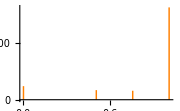

```mathematica
HP9 = Histogram[Rf9,{0.01},ChartStyle->Orange]
```

```mathematica
{T9a = Binarize[T9,{0,0.2}]}
```

{-Graphics-}

```mathematica
{T9b = Binarize[T9,{0.4,0.7}]}
```

{-Graphics-}

```mathematica
{T9c = Binarize[T9,{0.6,0.8}]}
```

{-Graphics-}

```mathematica
{Tdown = ImageMultiply[T5,0.5]}
```

{-Graphics-}

```mathematica
{Tup = ImageMultiply[T5,1.5]}
```

{-Graphics-}

```mathematica
(*--------------------Part 2--------------------*)
```

```mathematica
(*Problem 10*)
```

```mathematica
T10 := Import["mona.jpg"]
```

```mathematica
{CR,CG,CB} = ColorSeparate[T10]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{T10new = ImageMultiply[CB,1.5]}
```

{-Graphics-}

```mathematica
T10c = ColorCombine[{CR,CG,T10new}]
```

-Graphics-

```mathematica
{T10,T10c}
```

{-Graphics-,-Graphics-}

```mathematica
(*Problem 11*)
```

```mathematica
a := 0.8
```

```mathematica
f1[x_]:=1 / 2 (1+1 / Tan[a*Pi / 2]*Tan[a Pi (x-1 /2)])
```

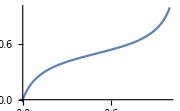

```mathematica
Plot[f1[x],{x,0,1}]
```

```mathematica
T10n1 =ImageApply[f1,T10]
```

-Graphics-

```mathematica
{T10,T10n1}
```

{-Graphics-,-Graphics-}

```mathematica
T10gl:=ColorConvert[T10,"Grayscale"]
```

```mathematica
T10ngl :=ColorConvert[T10n1,"Grayscale"]
```

```mathematica
T10gd=ImageData[T10gl];
```

```mathematica
T10nd=ImageData[T10ngl];
```

```mathematica
Mf=Flatten[T10gd];
```

```mathematica
Mnf=Flatten[T10nd];
```

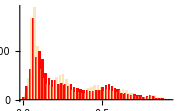

```mathematica
HM=Histogram[Mf,{0.01},ChartStyle->{Red,Opacity[0.5]}]
```

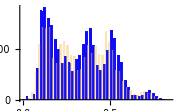

```mathematica
HMn=Histogram[Mnf,{0.01},ChartStyle->{Blue,Opacity[0.5]}]
```

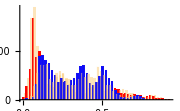

```mathematica
Show[HM,HMn]
```

```mathematica
{T10eq=HistogramTransform[T10]}
```

{-Graphics-}

```mathematica
{MRE,MGE,MBE}=ColorSeparate[T10eq]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{MR,MG,MB}=ColorSeparate[T10]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{MGnew=HistogramTransform[MGE]}
```

{-Graphics-}

```mathematica
a=1
```

1

```mathematica
f2[x_]:=x+x (1-x)*a
```

```mathematica
{MbN =ImageApply[f2,MB]}
```

{-Graphics-}

```mathematica
{Monanew=ColorCombine[{MR,MGnew,MbN}]}
```

{-Graphics-}

```mathematica
(*Problem 12*)
```

```mathematica
P1=Import["pill1.jpg"]
```

-Graphics-

```mathematica
P2=Import["pill2.jpg"]
```

-Graphics-

```mathematica
{PG1=ColorConvert[P1,"Grayscale"],PG2=ColorConvert[P2,"Grayscale"]}
```

{-Graphics-,-Graphics-}

```mathematica
DP1P2=ImageDifference[PG1,PG2]
```

-Graphics-

```mathematica
Result=ColorNegate[DP1P2]
```

-Graphics-

```mathematica
(*Problem 13*)
```

```mathematica
{Pirat1=Import["pirat.gif"]}
```

{-Graphics-}

```mathematica
{Pirat=RemoveAlphaChannel[Pirat1]}
```

{-Graphics-}

```mathematica
DimP=ImageDimensions[Pirat]
```

{300,180}

```mathematica
xPir=DimP[[1]]
```

300

```mathematica
yPir=DimP[[2]]
```

180

```mathematica
Pirat=ImagePartition[Pirat,{xPir /2,yPir}]
```

{{-Graphics-,-Graphics-}}

```mathematica
Part1=Pirat[[1]][[1]]
```

-Graphics-

```mathematica
Part2=Pirat[[1]][[2]]
```

-Graphics-

```mathematica
Part1G=ColorConvert[Part1,"Grayscale"]
```

-Graphics-

```mathematica
Part2G=ColorConvert[Part2,"Grayscale"]
```

-Graphics-

```mathematica
Diff=ImageDifference[Part1G,Part2G]
```

-Graphics-

```mathematica
DiffN=ColorNegate[Diff]
```

-Graphics-

```mathematica
{Part1,Part2,DiffN}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Problem 14*)
```

```mathematica
{Bu=Import["bush.jpg"]}
```

{-Graphics-}

```mathematica
Ar:=Import["arnold.jpg"]
```

```mathematica
Morph[t_]:=Blend[{Bu,Ar},t]
```

```mathematica
Mor = Table[Morph[t],{t,0,1,0.01}];
```

```mathematica
{ListAnimate[Mor,AnimationRunning->False]}
```

{}

```mathematica
(*--------------------Bonus Part--------------------*)
```

```mathematica
(*Problem 15*)
```